```mathematica
beta = 1/1.01;
gamma = Exp[0.005];
pistar = Exp[0.005];
zetap = 0.65;
nu=0;
rhophi = 0.94;
rholambda = 0.88;
rhoz=0.13;
sigmaphi = 0.01;
sigmalambda=0.01;
sigmaz = 0.01;
sigmar=0.01;
kappap=((1-zetap beta)/(zetap))(1 - zetap beta);
psip = (1 + (kappap/beta)(1+nu))^(-1);
xphi = -(kappap psip)/(beta(1 - psip rhophi));
xlambda = -(kappap psip)/(beta (1 -psip rholambda));
xz=-(rhoz psip)/(beta (1 - psip rhoz));
xepsilonr = - psip sigmar;
```

```mathematica
phi10= {{rhophi,0,0,0,0},{0,rholambda,0,0,0},{0,0,rhoz,0,0},{0,0,0,0,0},{xphi,xlambda,xz,xepsilonr,0}}
```

{{0.94,0,0,0,0},{0,0.88,0,0,0},{0,0,0.13,0,0},{0,0,0,0,0},{-0.766909,-0.621941,-0.123008,-0.00835135,0}}

```mathematica
Eigenvalues[ phi1]
```

Eigenvalues[phi1]

```mathematica
phiepsilon = {{sigmaphi,0,0,0},{0,sigmalambda,0,0},{0,0,sigmaz,0},{0,0,0,1},{0,0,0,0}}
```

{{0.01,0,0,0},{0,0.01,0,0},{0,0,0.01,0},{0,0,0,1},{0,0,0,0}}

```mathematica
phiepsilonn = phiepsilon.Transpose[phiepsilon];
DiscreteLyapunovSolve[phi10,phiepsilonn]
MatrixForm[%]
```

{{-0.000859107,0.,0.,0.,0.000619325},{0.,-0.000443262,0.,0.,0.000242601},{0.,0.,-0.000101719,0.,1.62659×10^-6},{0.,0.,0.,-1.,0.},{0.000619325,0.000242601,1.62659×10^-6,0.,-0.000748026}}

(-0.000859107 | 0. | 0. | 0. | 0.000619325
0. | -0.000443262 | 0. | 0. | 0.000242601
0. | 0. | -0.000101719 | 0. | 1.62659×10^-6
0. | 0. | 0. | -1. | 0.
0.000619325 | 0.000242601 | 1.62659×10^-6 | 0. | -0.000748026)

```mathematica
theta=Normal[0,Pi]
```

0

```mathematica
NormalDistribution[0,2]
```

NormalDistribution[0,2]

```mathematica
Expectation[x^{6},x \[Distributed] NormalDistribution[0,2]]
```

{960}

```mathematica
N[2Pi/8]
```

0.785398

```mathematica
Factorial[0]
```

1

```mathematica
func[x_]:=Sin[x];
tay[n_]:=Normal[Series[func[x],{x,0,n}]]
For[i=0,i<16,i++,Print[tay[i]]]
```

x

x

x

x-x^3/6

x-x^3/6

x-x^3/6+x^5/120

x-x^3/6+x^5/120

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000

x

x

x

x-x^3/6

x-x^3/6

x-x^3/6+x^5/120

x-x^3/6+x^5/120

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000

x

x

x

x-x^3/6

x-x^3/6

x-x^3/6+x^5/120

x-x^3/6+x^5/120

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000

x

x

x

x-x^3/6

x-x^3/6

x-x^3/6+x^5/120

x-x^3/6+x^5/120

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000

x

x

x

x-x^3/6

x-x^3/6

x-x^3/6+x^5/120

x-x^3/6+x^5/120

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000

0

x

x

x-x^3/6

x-x^3/6

x-x^3/6+x^5/120

x-x^3/6+x^5/120

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000

x

x

x-x^3/6

x-x^3/6

x-x^3/6+x^5/120

x-x^3/6+x^5/120

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800

Plot[{Sin[x],x},{x,-3 Pi,3 Pi},PlotLegends→{"sin(x)","n=1"},PlotRange→2]

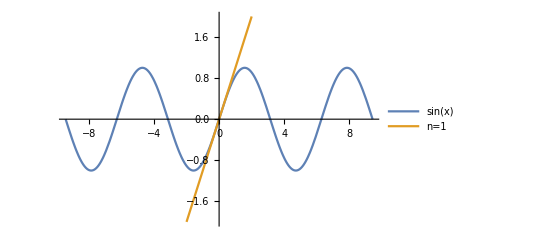

Plot[{Sin[x],x-x^3/6},{x,-3 Pi,3 Pi},PlotLegends→{"sin(x)","n=3"},PlotRange→2]

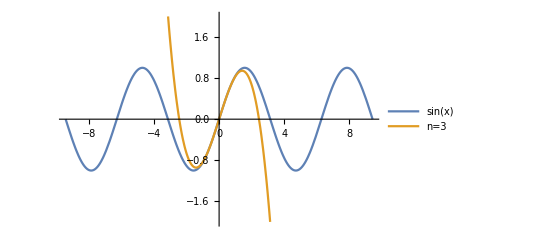

Plot[{Sin[x],x-x^3/6+x^5/120},{x,-3 Pi,3 Pi},PlotLegends→{"sin(x)","n=5"},PlotRange→2]

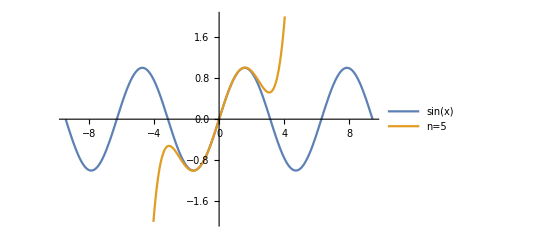

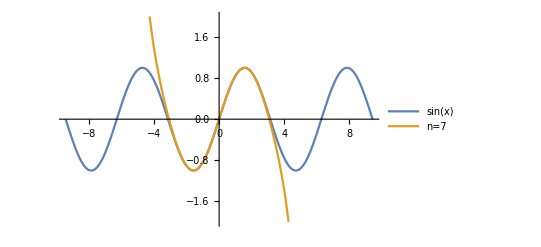

```mathematica
Plot[{Sin[x],x-x^3/6+x^5/120-x^7/5040},{x,-3 Pi,3 Pi},PlotLegends->{"sin(x)","n=7"},PlotRange->2]
```

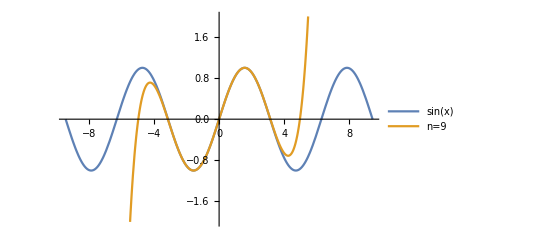

```mathematica
Plot[{Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880},{x,-3 Pi,3 Pi},PlotLegends->{"sin(x)","n=9"},PlotRange->2]
```

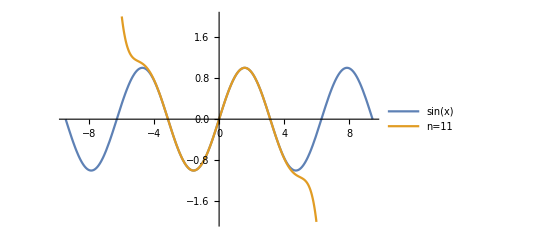

```mathematica
Plot[{Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800},{x,-3 Pi,3 Pi},PlotLegends->{"sin(x)","n=11"},PlotRange->2]
```

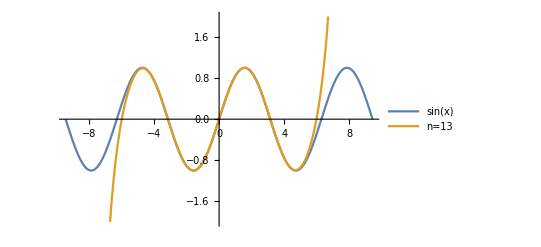

```mathematica
Plot[{Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800},{x,-3 Pi,3 Pi},PlotLegends->{"sin(x)","n=13"},PlotRange->2]
```

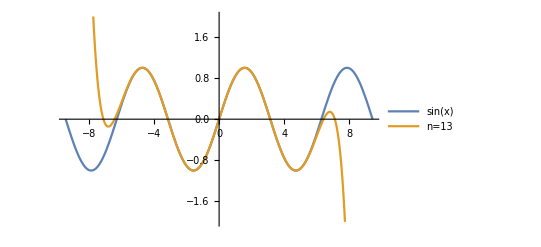

```mathematica
Plot[{Sin[x],x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000},{x,-3 Pi,3 Pi},PlotLegends->{"sin(x)","n=13"},PlotRange->2]
```

```mathematica
DiracDelta
```

DiracDelta

```mathematica
Integrate[DiracDelta[x-a]f[x],{x,-∞,∞}]
```

ConditionalExpression[f[a],a∈Reals]

```mathematica
(* 3.2 Normalization *)
1/(Sqrt[2Pi]σ)∫_(-∞)^∞ Exp[- x^2/(2 σ^2)]ⅆ x
```

ConditionalExpression[1/(√(1/σ^2) σ),Re[σ^2]>0]

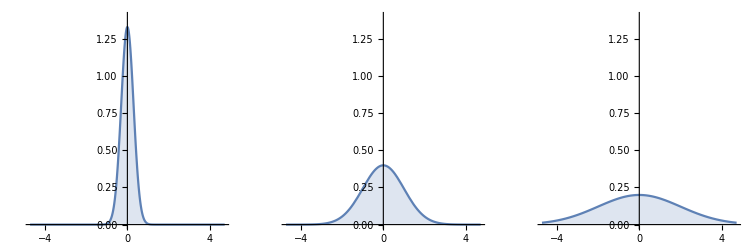

```mathematica
(* 增加σ的值会显著降低高斯核方程的振幅 *)
GK[x_,σ_] := 1/(Sqrt[2Pi] σ) Exp[(- x^2)/(2 σ^2)];
Block[{$DisplayFunction=Identity}, {p1,p2,p3} = Plot[GK[x,σ=#],{x,-1.5Pi,1.5Pi},PlotRange->{0,1.4}, Filling -> Bottom] & /@{0.3,1,2}];
GraphicsGrid[{{p1,p2,p3}}, ImageSize-> {750,250}]
```

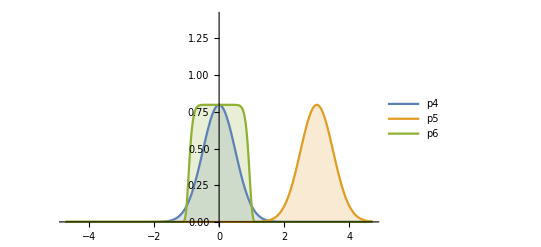

```mathematica
p4=GK[x,0.5];p5=GK[3-x,0.5];p6=GK[x^6,0.5];
Plot[{p4,p5,p6},{x,-1.5Pi,1.5Pi},PlotRange->{0,1.4},Filling->Bottom,PlotLegends->"Expressions"]
```

```mathematica
(* Cascade property *)
σ=.;
FullSimplify[∫_(-∞)^∞ GK[x,σ1] GK[α- x,σ2] ⅆx,{σ1 >0, σ2 >0, Im[σ1]==0, Im[σ2]==0}]
TeXForm[FullSimplify[∫_(-∞)^∞ GK[x,σ1] GK[α- x,σ2] ⅆx,{σ1 >0, σ2 >0, Im[σ1]==0, Im[σ2]==0}]]
```

(ⅇ^(-α^2/(2 (σ1^2+σ2^2))))/(√(2 π) √(σ1^2+σ2^2))

\frac{e^{-\frac{\alpha ^2}{2 \left(\text{$\sigma $1}^2+\text{$\sigma $2}^2\right)}}}{\sqrt{2 \pi } \sqrt{\text{$\sigma $1}^2+\text{$\sigma $2}^2}}

```mathematica
(* spatial extension *)
GK[5,1]//N
Integrate[GK[x,1],{x,5,∞}]//N
Integrate[GK[x,1],{x,-∞,-5}]//N
```

1.48672×10^-6

2.86652×10^-7

2.86652×10^-7

```mathematica
(* Dirac function *)
Limit[GK[0,σ],σ -> 0]
Limit[GK[1,σ],σ -> 0] (*将x=1变成其他值*)
FullSimplify[∫_(-∞)^∞ DiracDelta[x-a]f[x] ⅆ x, {Im[a]==0}]
FullSimplify[∫_(-∞)^∞ D[DiracDelta[x],{x,1}]f[x] ⅆ x]
FullSimplify[∫_(-∞)^∞ D[DiracDelta[x],{x,2}]f[x] ⅆ x]
```

∞

0

Piecewise[{{1, -1/2≤a≤1/2}, {0, True}}]

0

0

```mathematica
(* error function, or cumulative Gaussian function *)
σ = .;
error[x_, σ_] = FullSimplify[∫_(-∞)^(+x) 1/(Sqrt[2 Pi] σ) Exp[- y^2/(2 σ^2)] ⅆ y, {{Im[σ]==0, σ>0}}]
error[x_, σ_] = ∫_(-∞)^(+x) 1/(Sqrt[2 Pi] σ) Exp[- y^2/(2 σ^2)] ⅆ y
(* 或者也可以用Mathematica的程序Erf[] *)
```

1/2 (1+Erf[x/(√2 σ)])

ConditionalExpression[(1/(√(1/σ^2))+σ Erf[x/(√2 σ)])/(2 σ),Re[σ^2]>0]

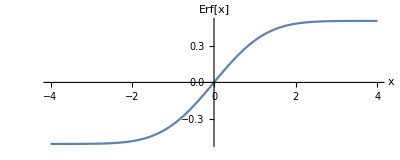

```mathematica
(* Error function*)
σ = 1.;
Plot[{1/2 Erf[x/(√2 σ)]},{x,-4,4},AspectRatio->.4, AxesLabel->{"x","Erf[x]"} ]
```

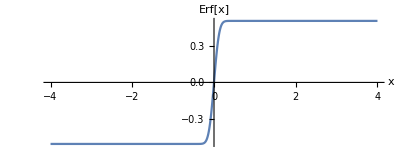

```mathematica
(* Error function*)
σ = 0.1;
Plot[{1/2 Erf[x/(√2 σ)]},{x,-4,4},AspectRatio->.4, AxesLabel->{"x","Erf[x]"} ]
```

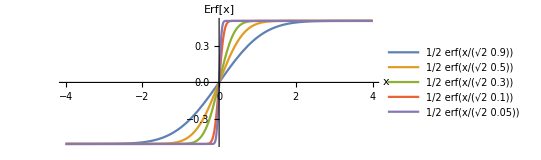

```mathematica
Plot[{1/2 Erf[x/(√2 0.9)],1/2 Erf[x/(√2 0.5)],1/2 Erf[x/(√2 0.3)],1/2 Erf[x/(√2 0.1)],1/2 Erf[x/(√2 0.05)]},{x,-4,4},AspectRatio->.4, AxesLabel->{"x","Erf[x]"},PlotLegends->"Expressions" ]
```

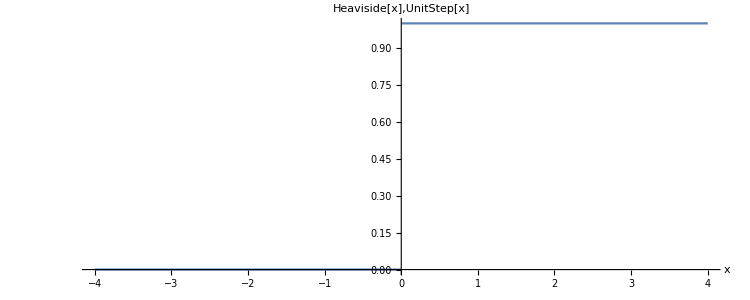

```mathematica
Plot[UnitStep[x],{x,-4,4},DisplayFunction->$DisplayFunction,AspectRatio->0.4,
AxesLabel->{"x","Heaviside[x],UnitStep[x]"},PlotStyle->Thick[0.15],ImageSize->{750,300}]
```

```mathematica
D[UnitStep[x],{x,1}]
FullSimplify[D[UnitStep[x],{x}],{x≠0}]
```

Piecewise[{{Indeterminate, x==0}, {0, True}}]

0

```mathematica
(* binomial coefficients *)
Expand[(x+y)^20]
TeXForm[Expand[(x+y)^20]]
Table[Binomial[20,n],{n,1,20}]
```

x^20+20 x^19 y+190 x^18 y^2+1140 x^17 y^3+4845 x^16 y^4+15504 x^15 y^5+38760 x^14 y^6+77520 x^13 y^7+125970 x^12 y^8+167960 x^11 y^9+184756 x^10 y^10+167960 x^9 y^11+125970 x^8 y^12+77520 x^7 y^13+38760 x^6 y^14+15504 x^5 y^15+4845 x^4 y^16+1140 x^3 y^17+190 x^2 y^18+20 x y^19+y^20

{20,190,1140,4845,15504,38760,77520,125970,167960,184756,167960,125970,77520,38760,15504,4845,1140,190,20,1}

x^{20}+20 x^{19} y+190 x^{18} y^2+1140 x^{17} y^3+4845 x^{16} y^4+15504 x^{15} y^5+38760 x^{14} y^6+77520 x^{13} y^7+125970 x^{12} y^8+167960 x^{11} y^9+184756 x^{10}
   y^{10}+167960 x^9 y^{11}+125970 x^8 y^{12}+77520 x^7 y^{13}+38760 x^6 y^{14}+15504 x^5 y^{15}+4845 x^4 y^{16}+1140 x^3 y^{17}+190 x^2 y^{18}+20 x y^{19}+y^{20}

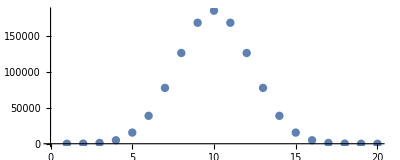

```mathematica
binomial1=ListPlot[Table[Binomial[20,n],{n,1,20}],PlotStyle->{PointSize[0.015]},AspectRatio->0.4];
binomial2=ListPlot3D[Table[Binomial[20,n]Binomial[20,m],{n,1,20},{m,1,20}],PlotRange->All];
GraphicsGrid[{{binomial1,binomial2}},ImageSize ->750]
```

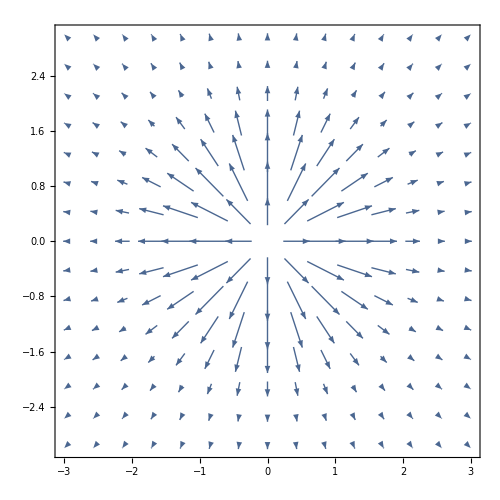

```mathematica
(* isotropic and anistropic *)
vk=-GK[x,1] GK[y,1];
vkx=D[vk,x];
vky=D[vk,y];
VectorPlot[{vkx,vky}, {x,-3,3},{y,-3,3},ImageSize->500,PlotRange->All]
```

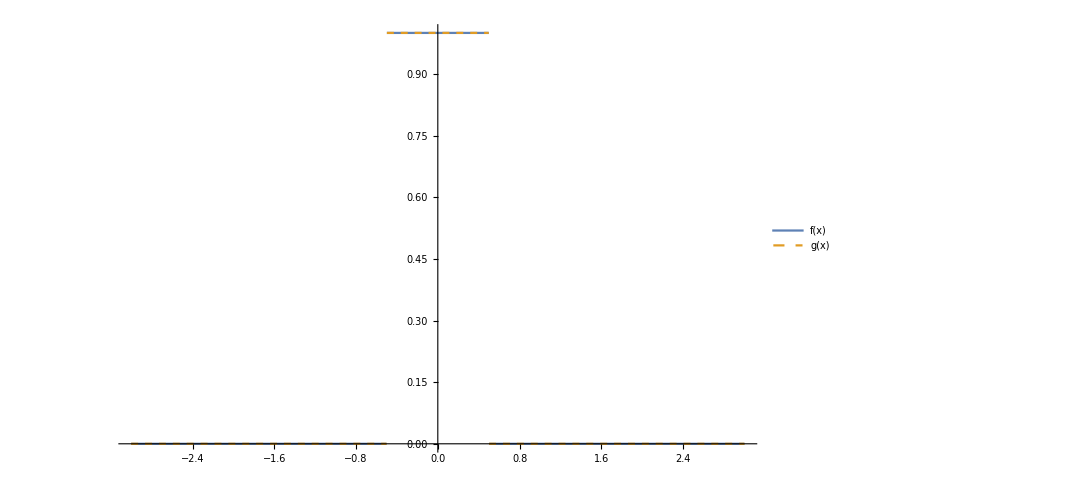

```mathematica
(* Central Limit Theorem *)
f[x_]:=UnitStep[1/2+x]+UnitStep[1/2-x]-1;
g[x_]:=UnitStep[1/2+x]+UnitStep[1/2-x]-1;
plotfg = Plot[{f[x],g[x]},{x,-3,3},PlotStyle->{Thick, Dashed},PlotLegends->"Expressions",ImageSize->800]
```

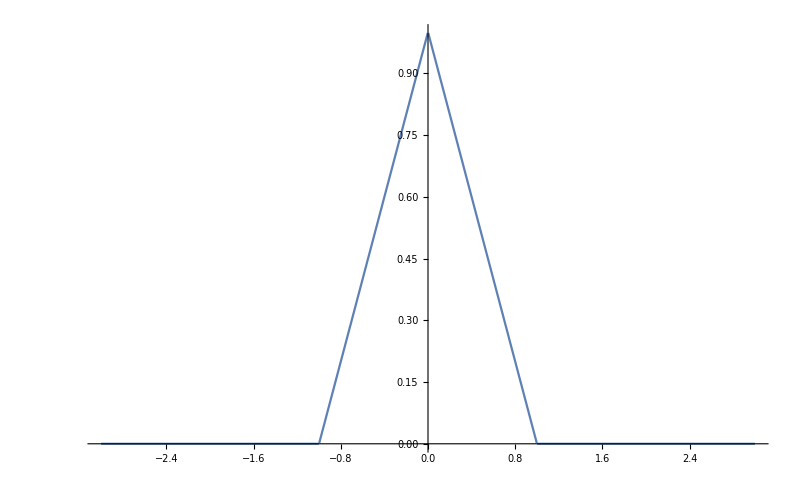

```mathematica
h1=FullSimplify[∫_(-∞)^∞ f[x]g[x-x1] ⅆx,{Im[x1]==0}];
plotfmultg=Plot[h1,{x1,-3,3}, PlotRange->All, ImageSize->800]
```

Piecewise[{{1/4 (3-4 x1^2), -1/2<x1<1/2}, {1/8 (3-4 x1-4 x1^2), x1==-1/2}, {1/8 (3+4 x1-4 x1^2), x1==1/2}, {1/8 (9-12 x1+4 x1^2), 1/2<x1<3/2}, {1/8 (9+12 x1+4 x1^2), -3/2<x1<-1/2}, {0, True}}]

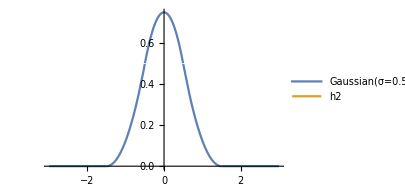

```mathematica
h2=∫_(-∞)^∞ (h1/.x1 -> x) g[x-x1]ⅆx
Plot[{h2,GK[x1,0.5]},{x1,-3,3},PlotRange->All,PlotStyle->{Dashing[{}],Dashing[{0.2,0.2}]},
ImageSize->300, PlotLegends->{"Gaussian(σ=0.5)","h2"}]
```

```mathematica
(* anistropic *)
GK[x_,y_,σx_,σy_]:=1/(2Pi σx σy) Exp[-(x^2/(2 σx^2)+y^2/(2 σy^2))];
σx=2;σy=1;
Block[
{$DisplayFunction=Identity},
p1=DensityPlot[GK[x,y,σx,σy],{x,-10,10},{y,-10,10},PlotPoints -> 50];
p2=Plot3D[GK[x,y,σx,σy],{x,-10,10},{y,-10,10},PlotRange->All,ColorFunction-> "BlueGreenYellow"];
p3=ContourPlot[GK[x,y,σx,σy],{x,-5,5},{y,-10,10}]];
GraphicsGrid[{{p1,p2,p3}},ImageSize ->750]
```

-Graphics-

```mathematica
(* Fourier transform *)
(* 自己写出傅里叶变换的程序 *)
σ = .;
FGK[ω_,σ_]:=Simplify[1/Sqrt[2Pi] ∫_(-∞)^∞ 1/(σ Sqrt[2 Pi]) Exp [-x^2/(2 σ^2)] Exp[I ω x]ⅆx, {σ>0, Im[σ] ==0}]
FGK[ω,σ]
```

(ⅇ^(-1/2 σ^2 ω^2))/(√(2 π))

```mathematica
(* 或者利用Mathematica自带的傅里叶变换程序*)
FullSimplify[FourierTransform[GK[x,σ],x,ω],σ >0]
```

(ⅇ^(-1/2 σ^2 ω^2))/(√(2 π))

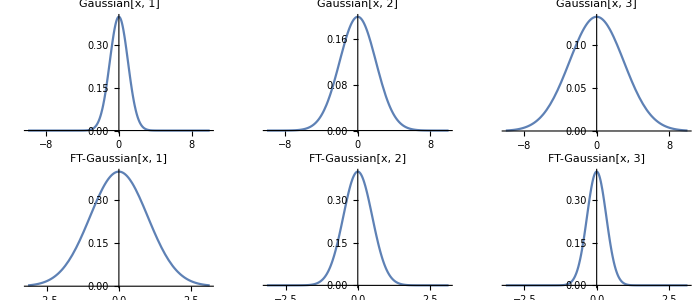

```mathematica
(* 原域中频率σ与傅里叶域中之间的关系 *)
(* 计算时间很长！*)
Block[{$DisplayFunction = Identity},
p1 = Table[Plot[GK[x,σ],{x,-10,10}, PlotRange->All,PlotLabel->"Gaussian[x, "<>ToString[σ] <>"]"], {σ,1,3}];
p2 = Table[Plot[FGK[ω,σ],{ω,-Pi,Pi}, PlotRange->All,PlotLabel->"FT-Gaussian[x, "<>ToString[σ] <>"]"], {σ,1,3}]];
GraphicsGrid[{p1,p2},ImageSize->{700,300}]
```